```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
{NN,RR} = Dimensions[S];
SubPlus[λ][ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];SubMinus[λ][ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
rates = { SubPlus[k][1] -> 1,SubMinus[k][1]->1,SubPlus[k] [2] ->1 , SubMinus[k][2]-> α,SubPlus[k][3]-> β,  SubMinus[k][3]->1}
J =Table[SubPlus[λ][ρ]- SubMinus[λ][ρ],{ρ,1,RR}];
J /.rates//MatrixForm
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→α,k_+[3]→β,k_-[3]→1}

(1-x[1]
-α x[1]+x[2]
-x[1]^3+β x[1]^2 x[2])

```mathematica
A = S.J;A /.rates//MatrixForm
```

(1-x[1]-α x[1]-x[1]^3+x[2]+β x[1]^2 x[2]
α x[1]+x[1]^3-x[2]-β x[1]^2 x[2])

```mathematica
SubStar[x] = Solve[A == 0, Table[x[i],{i,1,NN}]][[1]];SubStar[x]/.rates //FullSimplify
```

{x[1]→1,x[2]→(1+α)/(1+β)}

```mathematica
SubStar[vecx]=Table[x[i],{i,1,NN}]/. SubStar[x]/.rates
```

{1,(1+α)/(1+β)}

```mathematica
SubStar[J]= J /. SubStar[x]; SubStar[J]/.rates//FullSimplify
```

{0,(1-α β)/(1+β),(-1+α β)/(1+β)}

```mathematica
Subscript[A, (1)] = Together@FullSimplify@Grad[A,{x[1],x[2]}]/. SubStar[x];Subscript[A, (1)]/.rates
```

{{-4-α+(2 (1+α) β)/(1+β),1+β},{3+α-(2 (1+α) β)/(1+β),-1-β}}

```mathematica
DD = FullSimplify[Det[Subscript[A, (1)]]]/.rates
```

1+β

```mathematica
T =FullSimplify[ Tr[Subscript[A, (1)]]]/.rates //Together
```

(-5-α-4 β+α β-β^2)/(1+β)

```mathematica
Subscript[s, c]= Solve[T==0,α][[1]]//FullSimplify//Together;
Subscript[α, c]= Subscript[s, c][[1,2]]
```

(5+4 β+β^2)/(-1+β)

```mathematica
Eigenvalues[Subscript[A, (1)]]/.rates/. Subscript[s, c] //FullSimplify
```

{(1+β)^2/(√(-(1+β)^3)),(√(-(1+β)^3))/(1+β)}

```mathematica
Subscript[A, Δ]=A/.Table[x[i]->SubStar[vecx][[i]]+Δx[i],{i,1,NN}]/.rates;Collect[SubStar[A],{Δx[1],Δx[2]}]
```

{-x[1] k_-[1]-x[1] k_-[2]-x[1]^3 k_-[3]+k_+[1]+x[2] k_+[2]+x[1]^2 x[2] k_+[3],x[1] k_-[2]+x[1]^3 k_-[3]-x[2] k_+[2]-x[1]^2 x[2] k_+[3]}_*

```mathematica
γ=1
```

1

```mathematica
Subscript[A, δ]=(δα)^-γ Subscript[A, Δ]/. Δx[i_]->(δα)^γ δx[i]/.α -> Subscript[α, c]+δα//FullSimplify;Collect[Subscript[A, δ],δα]
```

{((-1+β) (1+β)^2 δx[1])/(-1+β^2)+δx[2]+β δx[2]+δα (((-1+β)^2 δx[1])/(-1+β^2)+(3 δx[1]^2)/(-1+β^2)+(4 β δx[1]^2)/(-1+β^2)+(2 β^2 δx[1]^2)/(-1+β^2)+(β^3 δx[1]^2)/(-1+β^2)+2 β δx[1] δx[2])+δα^2 (-(β δx[1]^2)/(-1+β^2)+(β^2 δx[1]^2)/(-1+β^2)-δx[1]^3+β δx[1]^2 δx[2]),(2 (1-β) δx[1])/(-1+β^2)+(3 (1-β) β δx[1])/(-1+β^2)+((1-β) β^2 δx[1])/(-1+β^2)-δx[2]-β δx[2]+δα (((-1+β) δx[1])/(-1+β^2)+((1-β) β δx[1])/(-1+β^2)-(3 δx[1]^2)/(-1+β^2)-(4 β δx[1]^2)/(-1+β^2)-(2 β^2 δx[1]^2)/(-1+β^2)-(β^3 δx[1]^2)/(-1+β^2)-2 β δx[1] δx[2])+δα^2 ((β δx[1]^2)/(-1+β^2)-(β^2 δx[1]^2)/(-1+β^2)+δx[1]^3-β δx[1]^2 δx[2])}

```mathematica
Subscript[M, 0]=Subscript[A, δ]/.δα->0//FullSimplify
```

{(1+β) (δx[1]+δx[2]),-((2+β) δx[1])-(1+β) δx[2]}

```mathematica
Subscript[F, δ]=Subscript[A, δ]/.δx[i_]->δx[i][t];
```

```mathematica
par = {β->3,δα->0.001}
```

{β→3,δα→0.01}

```mathematica
EQS=Table[D[δx[i][t],t]==Subscript[F, δ][[i]],{i,1,NN}]/.par;EQS//MatrixForm
IC={δx[1][0]==10,δx[2][0]==10};
vars = Table[δx[i][t],{i,1,NN}];
```

(δx[1]'[t]==1/8 δx[1][t] (32.04+0.6006 δx[1][t]-0.0008 (δx[1][t])^2)+δx[2][t]+3 (1+0.01 δx[1][t])^2 δx[2][t]
δx[2]'[t]==1/8 δx[1][t] (-40.04-0.6006 δx[1][t]+0.0008 (δx[1][t])^2)-(1+3 (1+0.01 δx[1][t])^2) δx[2][t])

```mathematica
Subscript[t, max]=100000;
sols=NDSolve[{EQS,IC},vars,{t,0,Subscript[t, max]}][[1]]
```

{δx[1][t]→InterpolatingFunction[{{0., 10000.}}, <>][t],δx[2][t]→InterpolatingFunction[{{0., 10000.}}, <>][t]}

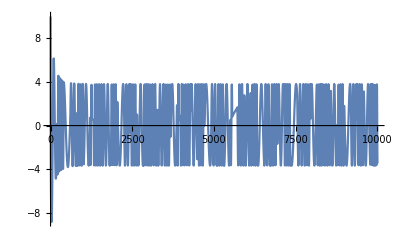

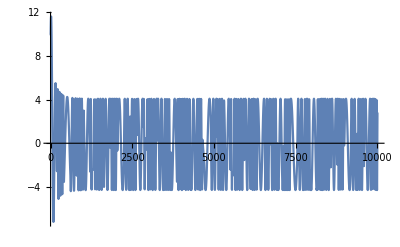

```mathematica
Plot[δx[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[δx[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

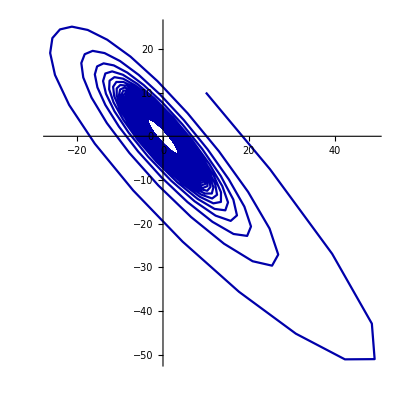

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

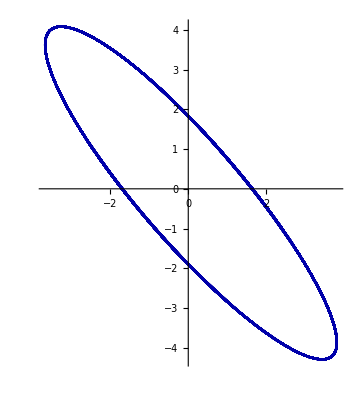

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,Subscript[t, max]*0.9,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

```mathematica
M = FullSimplify[Subscript[A, (1)]/.rates/.α->Subscript[α, c]];M//MatrixForm
```

(1+β | 1+β
-2-β | -1-β)

```mathematica
K = {{0,1},{1,0}};K//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
T=K.Inverse[Transpose[Eigenvectors[M]]];T//MatrixForm
```

(-(2+β)/(2 √(-1-β)) | -(1-√(-1-β)+β)/(2 √(-1-β))
(2+β)/(2 √(-1-β)) | (1+√(-1-β)+β)/(2 √(-1-β)))

```mathematica
T.M.Inverse[T]//FullSimplify//MatrixForm
```

(√(-1-β) | 0
0 | -√(-1-β))

```mathematica
II = {{0,1},{-1,0}};II//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
U=Inverse[Transpose[Eigenvectors[II]]];U//MatrixForm
```

(ⅈ/2 | 1/2
-ⅈ/2 | 1/2)

```mathematica
U.II.Inverse[U]//FullSimplify//MatrixForm
```

(ⅈ | 0
0 | -ⅈ)

```mathematica
vecδy = Table[δy[i],{i,1,NN}]
```

{δy[1],δy[2]}

```mathematica
vecδx = Inverse[T].U.vecδy//FullSimplify/.β->(ω^2-1)
```

{-(ⅈ √(-1-β) δy[1]+δy[2]+β δy[2])/(2+β),δy[2]}

```mathematica
Subscript[A, δy]= FullSimplify@Subscript[A, δ]/.Table[δx[i]->vecδx[[i]],{i,1,NN}]
```

{δy[2]+β δy[2] (1-(δα (ⅈ √(-1-β) δy[1]+δy[2]+β δy[2]))/(2+β))^2-1/((2+β) (-1+β^2))(ⅈ √(-1-β) δy[1]+δy[2]+β δy[2]) ((-1+β) ((1+β)^2+(-1+β) δα)-(δα (3+β (4-δα+β (2+β+δα))) (ⅈ √(-1-β) δy[1]+δy[2]+β δy[2]))/(2+β)-((-1+β^2) δα^2 (ⅈ √(-1-β) δy[1]+δy[2]+β δy[2])^2)/(2+β)^2),-1/((2+β) (-1+β^2))(ⅈ √(-1-β) δy[1]+δy[2]+β δy[2]) (-((-1+β) (2-δα+β (3+β+δα)))+(δα (3+β (4-δα+β (2+β+δα))) (ⅈ √(-1-β) δy[1]+δy[2]+β δy[2]))/(2+β)+((-1+β^2) δα^2 (ⅈ √(-1-β) δy[1]+δy[2]+β δy[2])^2)/(2+β)^2)-δy[2] (1+β (1-(δα (ⅈ √(-1-β) δy[1]+δy[2]+β δy[2]))/(2+β))^2)}

```mathematica
V= Inverse[U].T.Subscript[A, δy]//FullSimplify
```

{1/(2 √(-1-β) (2+β)^3 (1-β^2))ⅈ (-2 (-1+β) (1+β)^2 (2+β)^3 δy[2]+2 (2+β) δα (-(1+β)^2 (3+β+β^2) δy[1]^2+(1+β) δy[2] (2-3 β+β^3+(1+β) (-3-8 β+β^3) δy[2])-ⅈ √(-1-β) δy[1] (-(-1+β)^2 (2+β)+2 (1+β) (3+β (6+β)) δy[2]))-2 (-1+β^2) δα^2 (ⅈ √(-1-β) δy[1]^3+3 δy[1]^2 δy[2]+3 ⅈ √(-1-β) δy[1] δy[2]^2+δy[2]^3+β^4 δy[2]^3+β^3 δy[2] (δy[1]^2+δy[2]+2 ⅈ √(-1-β) δy[1] δy[2]+5 δy[2]^2)+β (ⅈ √(-1-β) δy[1]^3+2 ⅈ √(-1-β) δy[1] δy[2] (2+5 δy[2])+δy[2]^2 (2+5 δy[2])+δy[1]^2 (2+8 δy[2]))+β^2 (δy[1]^2 (1+6 δy[2])+δy[2]^2 (3+8 δy[2])+ⅈ √(-1-β) δy[1] δy[2] (2+9 δy[2])))),-1/((2+β) (-1+β^2))(ⅈ √(-1-β) δy[1]+(1+β) δy[2]) (-((-1+β) (2-δα+β (3+β+δα)))+(δα (3+β (4-δα+β (2+β+δα))) (ⅈ √(-1-β) δy[1]+(1+β) δy[2]))/(2+β)+((-1+β^2) δα^2 (ⅈ √(-1-β) δy[1]+(1+β) δy[2])^2)/(2+β)^2)-δy[2] (1+β (-1+(δα (ⅈ √(-1-β) δy[1]+(1+β) δy[2]))/(2+β))^2)}

```mathematica
O1 = FullSimplify@Series[V,{δα,0,1}]
```

{-ⅈ √(-1-β) δy[2]+1/(√(-1-β) (2+β)^2 (1-β^2))ⅈ (-(1+β)^2 (3+β+β^2) δy[1]^2+(1+β) δy[2] (2-3 β+β^3+(1+β) (-3-8 β+β^3) δy[2])-ⅈ √(-1-β) δy[1] (-(-1+β)^2 (2+β)+2 (1+β) (3+β (6+β)) δy[2])) δα+O[δα]^2,ⅈ √(-1-β) δy[1]+((ⅈ √(-1-β) δy[1]+(1+β) δy[2]) (2 β δy[2]+((-1+β)^2-((1+β) (3+β+β^2) (ⅈ √(-1-β) δy[1]+(1+β) δy[2]))/(2+β))/(-1+β^2)) δα)/(2+β)+O[δα]^2}

```mathematica
Subscript[F, 0]=Simplify@Coefficient[O1,δα,1]/.β->ω^2-1//FullSimplify
```

{1/(√(-ω^2) (-2+ω^2) (ω+ω^3)^2)(ⅈ ω^4 (3-ω^2+ω^4) δy[1]^2-ⅈ ω^2 δy[2] (4-3 ω^4+ω^6+(-2+ω) ω^2 (2+ω) (-1+ω^2+ω^4) δy[2])+√(-ω^2) δy[1] (4+ω^4 (-3+ω^2)-2 ω^2 (-2+4 ω^2+ω^4) δy[2])),((ⅈ √(-ω^2) δy[1]+ω^2 δy[2]) (1-2/ω^2+2 (-1+ω^2) δy[2]-((3-ω^2+ω^4) (ⅈ √(-ω^2) δy[1]+ω^2 δy[2]))/((-2+ω^2) (1+ω^2))))/(1+ω^2)}

```mathematica
Subscript[M, 0]=FullSimplify[V/.δα->0]/.δy[i_]->δy[i][t]
```

{-ⅈ √(-1-β) δy[2][t],ⅈ √(-1-β) δy[1][t]}

```mathematica
EQSy=Table[D[δy[i][t],t]==Subscript[M, 0][[i]],{i,1,NN}];EQS//MatrixForm
vars = Table[δy[i][t],{i,1,NN}];
```

(δx[1]'[t]==1/8 δx[1][t] (32.04+0.6006 δx[1][t]-0.0008 (δx[1][t])^2)+δx[2][t]+3 (1+0.01 δx[1][t])^2 δx[2][t]
δx[2]'[t]==1/8 δx[1][t] (-40.04-0.6006 δx[1][t]+0.0008 (δx[1][t])^2)-(1+3 (1+0.01 δx[1][t])^2) δx[2][t])

```mathematica
sol0 = DSolve[EQSy,vars,t][[1]]//FullSimplify/.β->ω^2-1
```

{δy[1][t]→C[1] Cosh[t √(-1-β)]-ⅈ C[2] Sinh[t √(-1-β)],δy[2][t]→C[2] Cosh[t √(-1-β)]+ⅈ C[1] Sinh[t √(-1-β)]}